# Penrose Encoding and graph visualization.

## Diana Itzel Vázquez Santiago. Emmanuel Isaac Juárez Caballero. Jesús Eduardo Hermosilla Díaz. Maestría en Inteligencia Artificial, generación 2021-2023

## Initializing Cells

```mathematica
(*Starting Executing Cells*)
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
FindExternalEvaluators["Python"]
session=StartExternalSession["Python"]
```

## Execution of the python code for the penrose Encoding.

```mathematica
u=Import["nuniversal.txt"]//ToExpression;
n1=450813704461563958982113775643437908;
n2=10389728107;
n=u;
ExternalEvaluate[session,File["penrose_encoding.py"]];
PenroseEncoding=ExternalEvaluate[session,"codificacion"];
execution=PenroseEncoding[n2];
```

TM after Penrose Coding:  R10R1R100R111RR1H

Instructions from TM

0            00 -> 00R

1            01 -> 10R

2            10 -> 01R

3           11 -> 100R

4          100 -> 111R

5           101 -> 00R

6           110 -> 01H

## Pre-processing rules for the instructions that came from Penrose Encoding

```mathematica
MT=Import["universal.txt"];
```

```mathematica
MT=StringDelete[StringSplit[Text[MT]⟦1⟧,","],{"[","]","'", " "}];
```

## Visualization using Multigraph2 with modified elements (originally taken from: https://mathematica.stackexchange.com/questions/201183/how-to-get-distinct-labels-on-parallel-edges-in-a-graph)

### MultiGraph2 implementation: A tool to visualize correctly multilabel graphs on Wolfram Mathematica

```mathematica
ClearAll[multiGraph2]
multiGraph2[vl_,elist_,elabels_,estyles_,o:OptionsPattern[Graph]]:=Module[{esf,edges,labels,styles,sorted=Transpose@SortBy[Transpose[{elist,elabels,estyles}],{PositionIndex[vl]@#[[1,1]]&,PositionIndex[vl]@#[[1,2]]&}]},{edges,labels,styles}={sorted[[1]],##&@@(RotateRight/@sorted[[2;;]])};
esf={First[styles=RotateLeft[styles]],GraphElementData["Arrow", "ArrowSize"->0.01][##]/. Arrowheads[ah_]:>Arrowheads[Append[ah,{.0003,.7,Graphics[Text[Framed[First[labels=RotateLeft[labels]],FrameStyle->None,Background->White]]]}]]}&;
Graph[vl,edges,EdgeShapeFunction->esf,o]]
```

### Table generation for associations in the graph in order to be functional with multigraph2

```mathematica
fn=ParallelTable[{{FromDigits[(StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin ,2]},{FromDigits[((StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin ),2]->FromDigits[((StringSplit[MT[[i]],"->"][[2]]//Characters)[[;;-3]]//StringJoin),2]},{StringJoin[(StringSplit[MT[[i]],"->"][[1]]//Characters)//Last,(StringSplit[MT[[i]],"->"][[2]]//Characters)[[-2]],(StringSplit[MT[[i]],"->"][[2]]//Characters)//Last]}},{i,1,Length[MT]}];
```

### Visualization of the graph using Gravity Embedding, a method to visualize more clearly the graph.

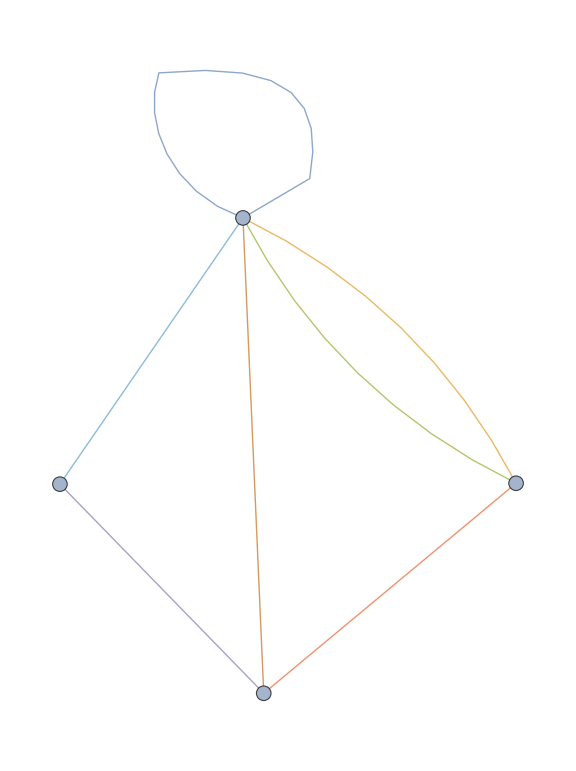

```mathematica
styles=ColorData[97]/@Range[Length[fn[[;;,3]]]];
g=multiGraph2[Flatten@Gather[(fn[[;;,1]]//Flatten)//DeleteDuplicates],fn[[;;,2]]//Flatten,fn[[;;,3]]//Flatten,styles,VertexSize->0.05,VertexLabels->Placed["Name",Center],ImageSize->Large, GraphLayout->"GravityEmbedding"]
```

#### Image List for the first 12 Turing Machines

```mathematica
imageList={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

#### Visualization of first 12 TM

```mathematica
ImageCollage[imageList]
```

-Graphics-

## Pre processing of the data in order to compile this in the UTM program for python

```mathematica
procesado=Table[{(*Estado inicial*)(StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin //ToExpression,
(*Valor que leo*)(StringSplit[MT[[i]],"->"][[1]]//Characters)//Last//ToExpression,
(*Valor que escribo*)(StringSplit[MT[[i]],"->"][[2]]//Characters)[[-2]]//ToExpression,
(*Movimiento*)(StringSplit[MT[[i]],"->"][[2]]//Characters)//Last//ToExpression,
(*Estado siguiente*)(StringSplit[MT[[i]],"->"][[2]]//Characters)[[;;-3]]//StringJoin//ToExpression
},
{i,1,Length[MT]}];
Export["procesado.csv", procesado]
```

procesado.csv

## Execution of the TM (Don’t execute this if the Machine has no halt, this would leead to an “infinite” execution)

### In order to execute the decoder for the UTM we need to introduce a number to execute U(n,m)=

```mathematica
ExternalEvaluate[session,File["decoderTM.py"]];
TMexecution=ExternalEvaluate[session,"execution"];
execution=TMexecution[231];
```

0 	 0 [1] 0 1 0 1 0 0 0 1 0 1 0 1 0 1 1 0

1 	 0 0 [0] 1 0 1 0 0 0 1 0 1 0 1 0 1 1 0

0 	 0 0 1 [1] 0 1 0 0 0 1 0 1 0 1 0 1 1 0

1 	 0 0 1 0 [0] 1 0 0 0 1 0 1 0 1 0 1 1 0

0 	 0 0 1 0 1 [1] 0 0 0 1 0 1 0 1 0 1 1 0

1 	 0 0 1 0 1 0 [0] 0 0 1 0 1 0 1 0 1 1 0

0 	 0 0 1 0 1 0 1 [0] 0 1 0 1 0 1 0 1 1 0

0 	 0 0 1 0 1 0 1 0 [0] 1 0 1 0 1 0 1 1 0

0 	 0 0 1 0 1 0 1 0 0 [1] 0 1 0 1 0 1 1 0

1 	 0 0 1 0 1 0 1 0 0 0 [0] 1 0 1 0 1 1 0

0 	 0 0 1 0 1 0 1 0 0 0 1 [1] 0 1 0 1 1 0

1 	 0 0 1 0 1 0 1 0 0 0 1 0 [0] 1 0 1 1 0

0 	 0 0 1 0 1 0 1 0 0 0 1 0 1 [1] 0 1 1 0

1 	 0 0 1 0 1 0 1 0 0 0 1 0 1 0 [0] 1 1 0

0 	 0 0 1 0 1 0 1 0 0 0 1 0 1 0 1 [1] 1 0

1 	 0 0 1 0 1 0 1 0 0 0 1 0 1 0 1 0 [1] 0

10 	 0 0 1 0 1 0 1 0 0 0 1 0 1 0 1 0 0 [0]

11 	 0 0 1 0 1 0 1 0 0 0 1 0 1 0 1 0 0 1 [0]

H 	 0 0 1 0 1 0 1 0 0 0 1 0 1 0 1 0 0 1 1 [0]

### Formato posible para la visualización de las máquinas de Turing.

```mathematica
a={{0,"[1]",0,0,0,1,1,0},
{0,0 ,"[0]",0,0,1,1,0},
{0,0,1,"[0]",0,1,1,0},
{0,0,1,0,"[0]",1,1,0},
{0 ,0,1,0,0,"[1]",1,0},
{0,0,1,0,0,0,"[1]",0},
{0,0,1,0,0,0,0,"[0]"},
{0,0,1,0,0,0,0,1,"[0]"},
{0,0,1,0,0,0,0,1,1,"[0]"}
};
```

```mathematica
a/.{"[0]"->Pink,"[1]"->Green,0->Yellow,1-> Yellow}//Grid
```

RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] |  | 
RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0.5, 0.5] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] |  | 
RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0.5, 0.5] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] |  | 
RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0.5, 0.5] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] |  | 
RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] |  | 
RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] |  | 
RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0.5, 0.5] |  | 
RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0.5, 0.5] | 
RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0.5, 0.5]